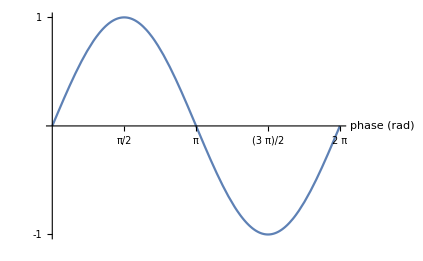

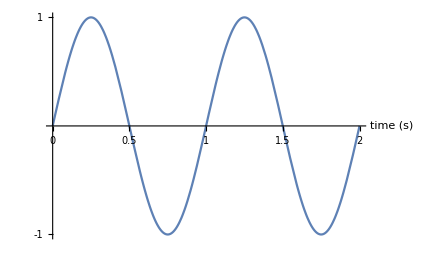

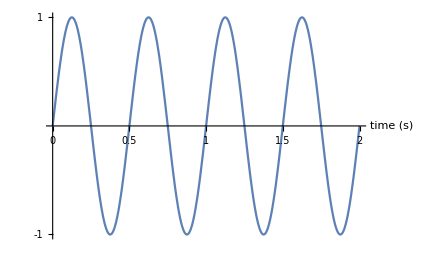

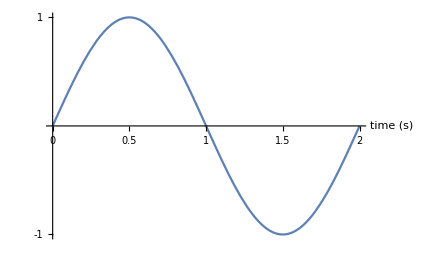

```mathematica
Plot[Sin[x],{x,0,2π},Ticks->{{π/2,π,3/2 π,2π},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"phase (rad)", None},AxesStyle->Directive["Label", 16]]
Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
Plot[Sin[4π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
Plot[Sin[1π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16]]
```

```mathematica
6.43*10^-4*80^2
```

4.1152

Lesson 2

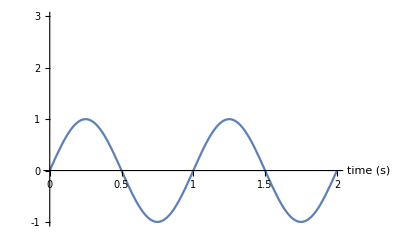

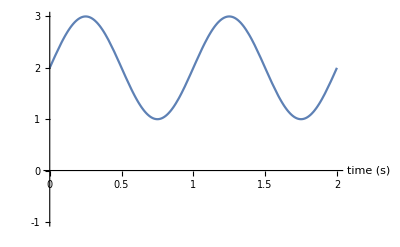

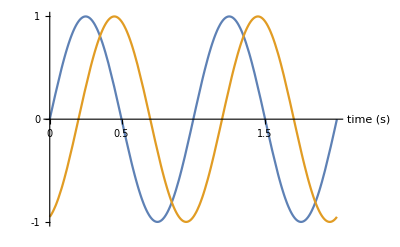

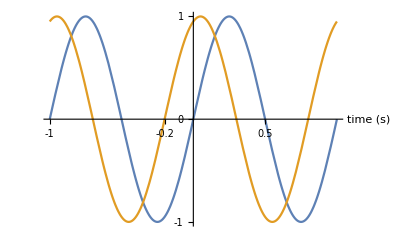

```mathematica
Plot[Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,0,1,2,3}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,3}]
Plot[2+Sin[2π t],{t,0,2},Ticks->{{0,0.5,1,1.5,2},{-1,0,1,2,3}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,3}]
Plot[{Sin[2π t],Sin[2π (t-0.2)]},{t,0,2},Ticks->{{0,0.2,0.5,1,1.5,2},{-1,0,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,1}]
Plot[{Sin[2π t],Sin[2π (t+0.2)]},{t,-1,1},Ticks->{{-1,-0.5,-0.2,0,0.5,1,1.5,2},{-1,0,1}},TicksStyle->Directive["Label", 14],AxesLabel->{"time (s)", None},AxesStyle->Directive["Label", 16],PlotRange->{-1,1}]
```

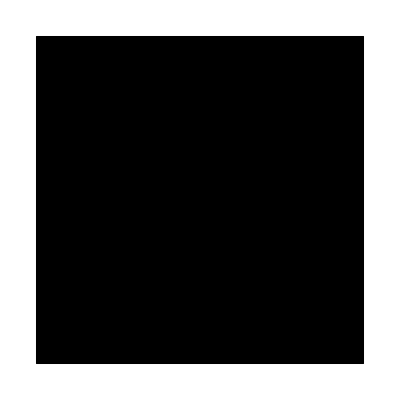

```mathematica
Graphics[{EdgeForm[{Thick, Black}],Rectangle[]}]
```

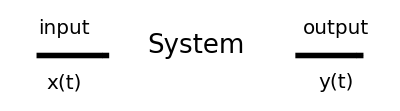

```mathematica
Graphics[{Style[Rectangle[{0,0},{20,10}],{EdgeForm[{Thick, Black}],Opacity[0]}],
Style[Arrow[{{-8,5},{0,5}}],Arrowheads[0.1],Thickness[0.01]],
Style[Arrow[{{20.5,5},{28,5}}],Arrowheads[0.1],Thickness[0.01]],
Text[Style["input",FontSize->20],{-5,8}],
Text[Style["x(t)",FontSize->20],{-5,2}],
Text[Style["output",FontSize->20],{25,8}],
Text[Style["y(t)",FontSize->20],{25,2}],
Text[Style["System",FontSize->26],{9.5,6}]
}]
```

```mathematica
Graphics[{Style[Line[{{0,2},{0,-5}}], Thick,Dashed],
Line[{{0,0},{3,-3}}],
Circle[{0,0},1,{-π/2,-.8}],
Text[Style["y",FontSize->23],{0.5,-1.5}],
Disk[{3,-3},0.3]
}]
```

-Graphics-